# Shockley-Queisser limit

The Shockley-Queisser limit is the upper theoretical limit for the efficiency of p-n junction solar cells. It plays an important role to estimate how far an experimental solar cell efficiency is from the maximum achievable theoretical efficiency.

source: William Shockley and Hans J.Queisser, J.Appl.Phys.32, 510 (1961); doi : 10.1063/1.1736034

## Physical model

Single cut-off frequency: for E ≥ hν effect otherwise no effect

p-n junction solar cell is at T_C = 0, surrounded by a blackbody at T = T_(s.)

Introduce finite T_C and replace surrounding body at T_S  by radiation coming from the sun at a small solid angle ω_s .

### Ultimate efficiency hypothesis

Each photon with E>hν_g produces 1 q_e at a voltage of V_g = hν_g/q_e

#### Formula check for incident power

```mathematica
Remove [h,ν,Ts,κ,c]
```

```mathematica
((2 π h) ∫_0^∞ ν^3/(exp((h ν)/(κ Ts))-1)ⅆν)/c^2
```

ConditionalExpression[(2 π^5 Ts^4 κ^4)/(15 c^2 h^3),Re[h/(Ts κ)]>0]

## Physical constants

Planck’s constant

```mathematica
h = QuantityMagnitude@UnitConvert[Quantity[1,"PlanckConstant"],"SIBase"]
```

6.62607×10^-34

speed of light

```mathematica
c = QuantityMagnitude@UnitConvert[Quantity[1,"SpeedOfLight"],"SIBase"]
```

299792458

Boltzmann constant

```mathematica
κ =  QuantityMagnitude@UnitConvert[Quantity[1,"BoltzmannConstant"],"SIBase"]
```

1.3806×10^-23

```mathematica
qe = QuantityMagnitude@UnitConvert[Quantity[1,"ElementaryCharge"],"SIBase"]
```

1.602177×10^-19

## Black-body Radiation

### Built - in

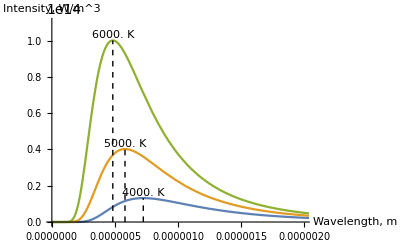

```mathematica
<<BlackBodyRadiation`
BlackBodyProfile[4000 Kelvin,5000 Kelvin,6000 Kelvin,PlotRange->{{0,2.0*10^-6},{0,1.1*10^14}},ImageSize->400]
```

### User - made

Bν (T) is the spectral radiance (the power per unit solid angle and per unit of area normal to the propagation) density of frequency ν radiation per unit frequency at thermal equilibrium at temperature T.

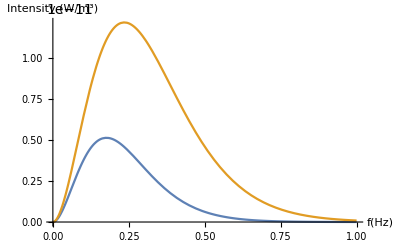

```mathematica
Remove[T,B]
B [T_]:=  (2h ν^3)/c^2 1/(Exp[((h ν)/(κ T))]-1);(*T=300;*)
(*Plot[Subscript[B, ν],{ν,1,10000},PlotRange->All]*)
Plot[{B[300],B[400]},{ν, 0 10^13,10 10^13},AxesLabel->{"f(Hz)","Intensity (W/m^3)"}]
```

## useful parameters for the calculation

```mathematica
Subscript[E, g]=Subscript[hν, g]=q Subscript[V, g]
Subscript[x, g]=Subscript[E, g]/(κ Ts)
Subscript[x, c]=Tc/Ts
```

### Surrounding temperature

```mathematica
Ts = 6000;
```

## Calculation & Result

### Output power from the solar cell

Qs: # of frequency quanta greater than v_g incident per unit time per unit area for black body radiation

```mathematica
Qs=((2 π)/c^2) ∫_Subscript[v, g]^∞ ν^2/(exp((h ν)/(κ Ts))-1)ⅆν
```

Putting (h ν)/(κ Ts)=x;

```mathematica
Qs[xg_]:=((2 π)/c^2)((κ Ts)/h)^3 ∫_xg^∞ x^2/(Exp[x]-1)ⅆx
```

Output power = h ν_g AQ_s, from Ultimate efficiency hypothesis

### Incident Power

```mathematica
Ps=((2 πh) ∫_0^∞ ν^3/(exp[(h ν)/(κ Ts)]-1)ⅆν)/c^2
```

after variable changed to x

```mathematica
Ps=((2 π)/(c^2 h^3)) (κ Ts)^4∫_0^∞ x^3/(Exp[x]-1)ⅆx
```

7.3488×10^7

Ultimate efficiency function

```mathematica
u[xg_]:= κ Ts xg  Qs [xg]/Ps (*Qs[xg]/Ps*);
```

~44% maximum efficiency achievable

```mathematica
u[2.2]//AbsoluteTiming
```

{5.85332,0.438691}

## As a function of xg

```mathematica
maxeffdata = Transpose[{
Range[0,10,.5],
100*u[#]&/@Range[0,10,.5]
}];
```

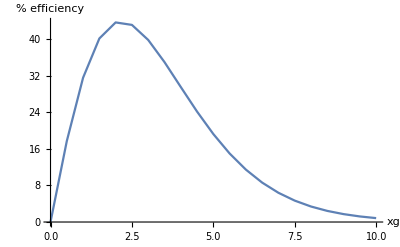

```mathematica
ListLinePlot[maxeffdata,PlotRange->All,AxesLabel->{"xg",  "% efficiency"}]
```

## As a function of bandgap

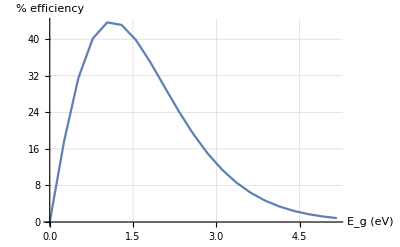

```mathematica
maxeffdataEn = Transpose[{
κ Ts Range[0,10,.5]/qe,
100*u[#]&/@Range[0,10,.5]
}];
ListLinePlot[maxeffdataEn,GridLines->Automatic,AxesLabel->{"E_g (eV)",  "% efficiency"}]
```

At the bandgap of 1.1 eV ~44% maximum efficiency achievable

Further Explorations

Calculation of η_max with T_C = 300 K.

Radiative recombination & lifetime consideration.

Authorship information

Suman Banerjee

2017/06/23

suman.banerjeee@gmail.com